1.24

a.

```mathematica
0.5/(1-(1-0.5)^2)
```

0.666667

c.

```mathematica
D[p/(1-(1-p)^2),p]//FullSimplify
```

1/(-2+p)^2

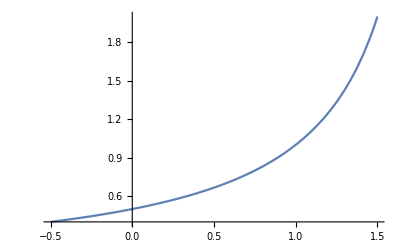

```mathematica
Plot[p/(1-(1-p)^2),{p,-0.5, 1.5}]
```

1.34

```mathematica
1/2*2/3+1/2*3/5
```

19/30

```mathematica
(1/2*2/3)/(19/30)
```

10/19

1.51

```mathematica
Sum[(Binomial[5,x]*Binomial[25, 4-x])/Binomial[30,4.],{x,0,3}]
```

0.999818

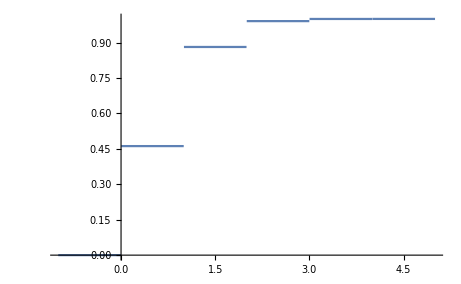

```mathematica
Plot[Piecewise[{{0,x<0},
{0.461595, 0<x≤ 1},
{0.881266, 1 < x ≤ 2},
{0.990695, 2 < x ≤ 3},
{0.999818, 3 < x ≤ 4},
{1, x > 4}
}],{x,-1,5}]
```